```mathematica
Clear["Global`*"]
```

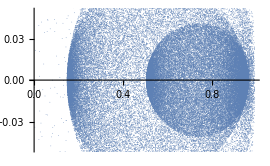
```mathematica
nuvem=Show[-Graphics-,Frame-> True];
```

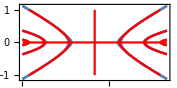
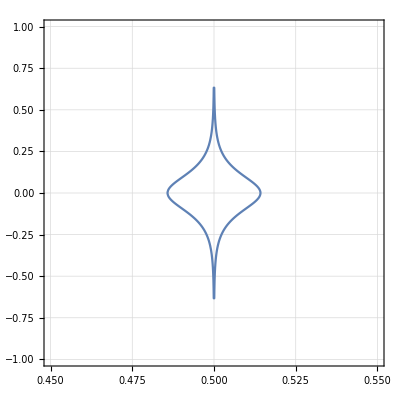
```mathematica
bands=Show[-Graphics-,-Graphics-];
```

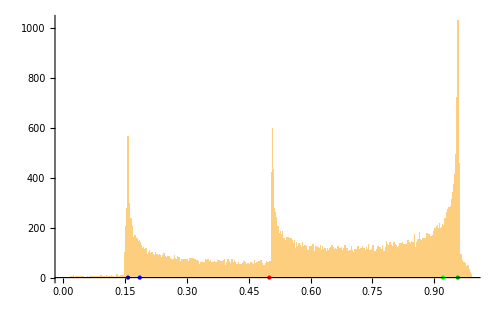
```mathematica
hist=-Graphics-;
```

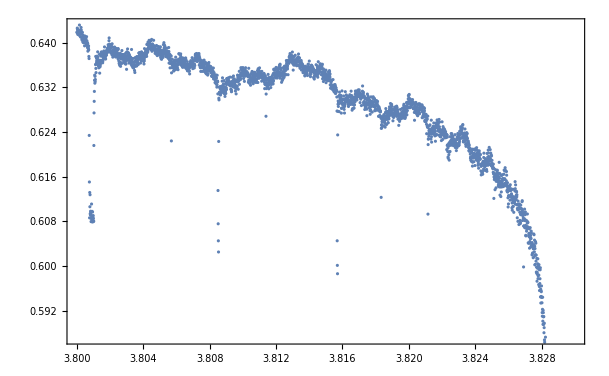
```mathematica
media = -Graphics-;
```

```mathematica
meanvalues =Table[imag=y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7;

real = x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7;

ys =FullSimplify[ Solve[imag==0,y]];
xs = Solve[imag==0,x];

xfmeio[x_] = real/.y-> ys⟦1,1,2⟧/.μ-> μ0;

pmeio1 = FindMinimum[{xfmeio[x],0.1≤x≤0.25}, x]⟦1⟧;
pmeio2= FindMinimum[{xfmeio[x],0.4≤x≤0.5}, x]⟦1⟧;
pmeio3 =FindMaximum[{xfmeio[x],0.9≤x≤0.99}, x]⟦1⟧;

Dmap3=D[real/.y-> 0,x];
y3null=Sort[xs/.{y-> 0,μ-> μ0}];

f = 5;
f1 =Interpolation[Table[{real/. {μ-> μ0,y-> 0},Abs[1/Dmap3]/. {μ-> μ0}},{x,0,(1-10^-f)y3null⟦1,1,2⟧,10^-f}]];
f2 =Interpolation[Table[{real/. {μ-> μ0,y-> 0},Abs[1/Dmap3]/. {μ-> μ0}},{x,(1+10^-f)y3null⟦1,1,2⟧,(1-10^-f)y3null⟦2,1,2⟧,10^-f}]];
f3 =Interpolation[Table[{real/. {μ-> μ0,y-> 0},Abs[1/Dmap3]/. {μ-> μ0}},{x,(1+10^-f)y3null⟦2,1,2⟧,(1-10^-f)y3null⟦3,1,2⟧,10^-f}]];
f4 =Interpolation[Table[{real/. {μ-> μ0,y-> 0},Abs[1/Dmap3]/. {μ-> μ0}},{x,(1+10^-f)y3null⟦3,1,2⟧,(1-10^-f)y3null⟦4,1,2⟧,10^-f}]];

pesototal[x_] = Piecewise[{{f1[x],x< pmeio1},{f1[x]+f2[x]+f3[x],pmeio1<x< pmeio2},{f1[x]+f2[x]+f3[x]+f4[x],pmeio2< x< pmeio3}}];

Mean[{pmeio1, pmeio2, pmeio3}];

NIntegrate[pesototal[x]x,{x,0,pmeio3}, (*Exclusions->{pmeio1,pmeio2,pmeio3}*),MaxRecursion->50,Method->"GlobalAdaptive"]/NIntegrate[pesototal[x],{x,0,pmeio3},(*Exclusions->{pmeio1,pmeio2,pmeio3}*),MaxRecursion->50, Method->"GlobalAdaptive"],


{μ0,{3.8255}}]
```

```mathematica
meanpeakvalues={};
```

```mathematica
meanvalues =Table[imag=y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7;

real = x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7;

ys =FullSimplify[ Solve[imag==0,y]];
xs = Solve[imag==0,x];

xfmeio[x_] = real/.y-> ys⟦1,1,2⟧/.μ-> μ0;

pmeio1 = FindMinimum[{xfmeio[x],0.1≤x≤0.25}, x]⟦1⟧;
pmeio2= FindMinimum[{xfmeio[x],0.4≤x≤0.5}, x]⟦1⟧;
pmeio3 =FindMaximum[{xfmeio[x],0.9≤x≤0.99}, x]⟦1⟧;

AppendTo[meanpeakvalues, {μ0,Mean[{pmeio1,pmeio2,pmeio3}]}];

y0 = 10^-3;
Dmap3=D[real/.y-> y0,x];
y3null=Sort[xs/.{y-> y0,μ-> μ0}];

f = 3;
f1 =Interpolation[Table[{real/. {μ-> μ0,y-> y0},Abs[1/Dmap3]/. {μ-> μ0}},{x,0,(1-10^-f)y3null⟦1,1,2⟧,10^-f}], InterpolationOrder->2];
f2 =Interpolation[Table[{real/. {μ-> μ0,y-> y0},Abs[1/Dmap3]/. {μ-> μ0}},{x,(1+10^-f)y3null⟦1,1,2⟧,(1-10^-f)y3null⟦2,1,2⟧,10^-f}],InterpolationOrder->2];
f3 =Interpolation[Table[{real/. {μ-> μ0,y-> y0},Abs[1/Dmap3]/. {μ-> μ0}},{x,(1+10^-f)y3null⟦2,1,2⟧,(1-10^-f)y3null⟦3,1,2⟧,10^-f}],InterpolationOrder->2];
f4 =Interpolation[Table[{real/. {μ-> μ0,y-> y0},Abs[1/Dmap3]/. {μ-> μ0}},{x,(1+10^-f)y3null⟦3,1,2⟧,(1-10^-f)y3null⟦4,1,2⟧,10^-f}],InterpolationOrder->2];

pesototal[x_] = Piecewise[{{f1[x],x< (1-10^-f) pmeio1},{f1[x]+f2[x]+f3[x],(1+10^-f)pmeio1<x< (1-10^-f)pmeio2},{f1[x]+f2[x]+f3[x]+f4[x],(1+10^-f)pmeio2< x< (1-10^-f)pmeio3}}];

fintx=Interpolation[Table[{x,x pesototal[x]},{x,0,1,1/10000}]];

fint = Interpolation[Table[{x, pesototal[x]},{x,0,1,1/10000}]];

Integrate[fintx[x]  ,{x,0,1}]/Integrate[fint[x],{x,0,1}],

{μ0,Table[i, {i, 3.810, 3.8290, 0.001}]}]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1/10000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1/5000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0.627617,0.626924,0.626698,0.626646,0.62637,0.625534,0.625123,0.624482,0.624824,0.624061,0.623463,0.62286,0.623153,0.622417,0.621774,0.622014,0.621486,0.620556,0.620996,0.620323}

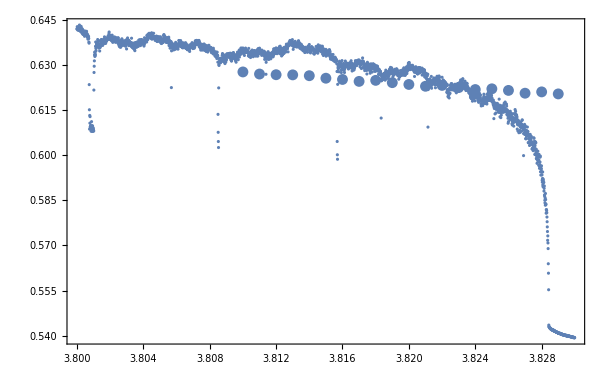

```mathematica
Show[media,ListPlot[meanvaluesμ], PlotRange-> All]
```

```mathematica
meanvaluesμ = Inner[List,Table[i, {i, 3.810, 3.8290, 0.001}],Flatten[meanvalues],List];
```

Passo do Table 1/10000, Method → Hermite, InterpolationOrder→ 1, f = 5

```mathematica
meanvaluesμ0 = meanvaluesμ;
```

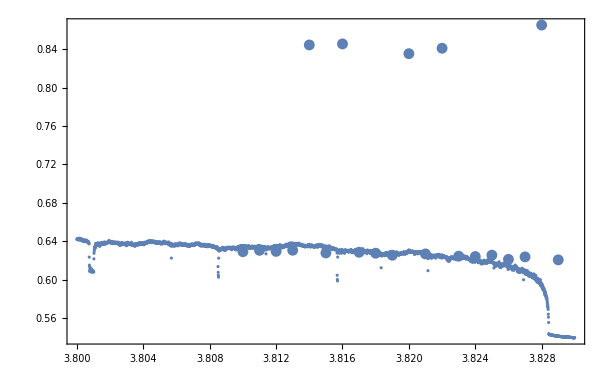

```mathematica
Show[media,ListPlot[meanvaluesμ], PlotRange-> All]
```

Passo do Table 1/10000, f= 5

```mathematica
meanvaluesμ1 = meanvaluesμ;
```

```mathematica
Show[media,ListPlot[meanvaluesμ1], PlotRange-> All]
```

-Graphics-

Passo do Table 1/15000, Method → Hermite, InterpolationOrder→ 1, f = 5

```mathematica
meanvaluesμ2 = meanvaluesμ;
```

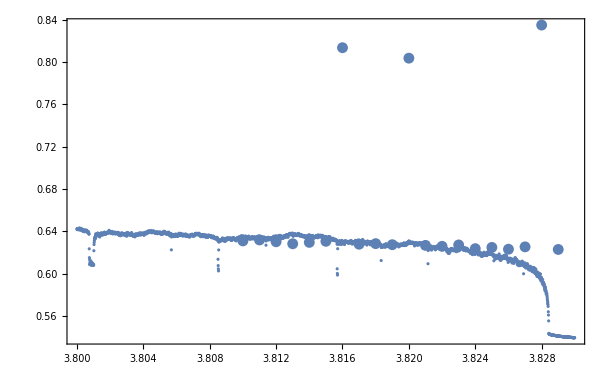

```mathematica
Show[media,ListPlot[meanvaluesμ2], PlotRange-> All]
```

Passo do Table 1/15000, f = 5

```mathematica
meanvaluesμ3 = meanvaluesμ;
```

```mathematica
Show[media,ListPlot[meanvaluesμ3], PlotRange-> All]
```

-Graphics-

Passo do Table 1/20000, f = 5

```mathematica
meanvaluesμ4 = meanvaluesμ;
```

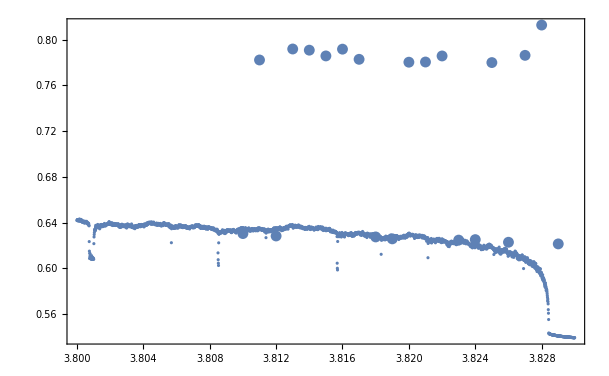

```mathematica
Show[media,ListPlot[meanvaluesμ4], PlotRange-> All]
```

Passo do Table 1/10000, f = 4, InterpolationOrder→ 2 (f1,f2,f3,f4)

```mathematica
meanvaluesμ5= meanvaluesμ;
```

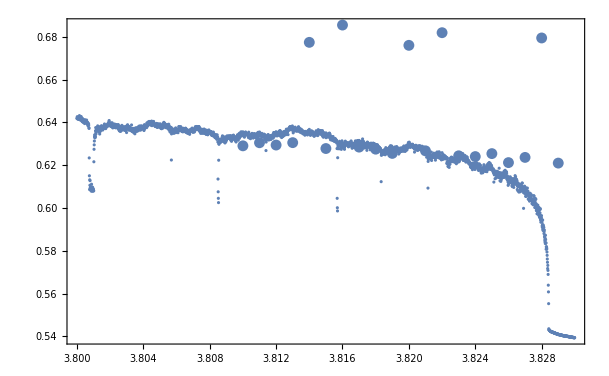

```mathematica
Show[media,ListPlot[meanvaluesμ5], PlotRange-> All]
```

Passo do Table 1/10000, f = 2, InterpolationOrder→ 2 (f1,f2,f3,f4)

```mathematica
meanvaluesμ6= meanvaluesμ;
```

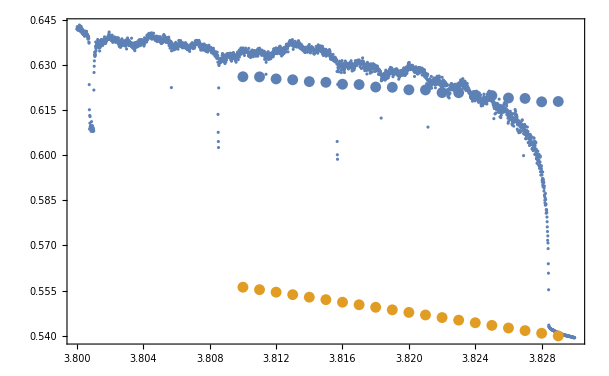

```mathematica
Show[media,ListPlot[{meanvaluesμ6, meanpeakvaluesμ}], PlotRange-> All]
```

```mathematica
fintx=Interpolation[Table[{x,x pesototal[x]},{x,0,1,1/20000}], InterpolationOrder->1];

fint = Interpolation[Table[{x, pesototal[x]},{x,0,1,1/20000}], InterpolationOrder->1];
```

```mathematica
Integrate[fintx[x]  ,{x,0,1}]/Integrate[fint[x],{x,0,1}]
```

0.625148

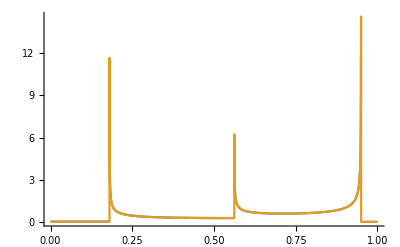

```mathematica
Plot[{pesototal[x],fint[x]},{x,0,1}, PlotRange->All]
```

de 3.820 até 3.8250

```mathematica
{0.6418505665246708,0.6414655673406652,0.6414471908798226,0.6387875791903774,0.6409395479714172,0.640993623311842,0.6405405520795745,0.640441917016401,0.640096898407154,0.6400625564251019,0.6408845140235809}
```

```mathematica
Table[Sort[xs/.{y-> 0,μ-> μ0}],{μ0, {3.820,3.8250,0.0005}}]
```

{{{x→0.042336},{x→0.154877},{x→0.330402},{x→1/2},{x→0.669598},{x→0.845123},{x→0.957664}},{{x→0.0422074},{x→0.154629},{x→0.329741},{x→1/2},{x→0.670259},{x→0.845371},{x→0.957793}},{{x→-175.917-179.228 ⅈ},{x→-175.917+179.228 ⅈ},{x→0.5-31.6188 ⅈ},{x→0.5+31.6188 ⅈ},{x→1/2},{x→176.917-179.228 ⅈ},{x→176.917+179.228 ⅈ}}}

```mathematica
Table[i, {i, 3.800, 3.8250, 0.001}]
```

{3.8,3.801,3.802,3.803,3.804,3.805,3.806,3.807,3.808,3.809,3.81,3.811,3.812,3.813,3.814,3.815,3.816,3.817,3.818,3.819,3.82,3.821,3.822,3.823,3.824,3.825}

```mathematica
3
```